```mathematica
Quit[];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
```

# Problem 3: ergodic metric

## System description

The system could be a spring-mass-damper. This will provide intuition about how damping affects ergodicity. In the phase plane, the trajectory is circular when there is no damping.

State space model

```mathematica
A={{0,1},{-1,-b}};
ssm=x'[t]==A.x[t];
n=First[Dimensions[A]];
```

Initial conditions, timestep size, and terminal time

```mathematica
ICs=x[0]=={{0},{1}};
dt=0.1;(*the system has natural frequency 1, choose dt appropriately*)
T=100;
```

Distribution w.r.t. which we care about ergodicity

```mathematica
μ={{0},{0}};
Σ=DiagonalMatrix[{2,2}];
ϕ[x_]:=Det[2 Pi Σ]^-1 Exp[-1/2(x-μ)ᵀ.Inverse[Σ].(x-μ)][[1,1]];
```

## Ergodic metric

Functions that build up the ergodic metric

```mathematica
K=4;(*length of Fourier expansion, consider accuracy vs computation time*)
L1=10;(*length of dimension 1 of state????*)
L2=10;(*length of dimension 2 of state????*)
L={{L1},{L2}};
Λ[k_]:=(1+Norm[k,2]^2)^(-((n+1)/2));
h[k_]:=(∫_0^L1 ∫_0^L2 Cos[((k[[1,1]] Pi)/L1) x1]^2 Cos[((k[[1,1]] Pi)/L1)x2]^2 ⅆx1ⅆx2)^(1/2);
Fk[k_,xt_]:=1/h[k]∏_(i=1)^n Cos[(k[[i,1]] Pi)/L[[i,1]] xt[[i,1]]];
ck[k_,xt_]:=1/T∫_0^T (1/h[k]∏_(i=1)^n Cos[(k[[i,1]] Pi)/L[[i,1]] xt[[i,1]][t]] )ⅆt
ϕk[k_]:=∫_0^L1 ∫_0^L2 ϕ[{{x1},{x2}}] Fk[k,{{x1},{x2}}]ⅆx2ⅆx1;
```

Function for evaluating the ergodic metric for a state trajectory

```mathematica
ErgodicMetric[x_]:=Module[{ϵ},ϵ=0;
For[i=0,i<K,++i;
For[j=0,j<K,++j;
ckij=N[ck[{{i},{j}},{{x[[1,1]]},{x[[2,1]]}}]]//Quiet;(*surpressing recursion warning*)
ϕkij=N[Re[ϕk[{{i},{j}}]]];
ϵ+=Λ[{{i},{j}}] (Abs[ckij-ϕkij])^2(*;Print[ϵ]*)]];Return[ϵ]];
```

## Evaluate ergodic metric for a range of b values, with T=100 s

```mathematica
ϵlistGivenT={};
For[damping=-1.1,damping<1,damping=damping+0.1;
Print["damping = ",damping];
sol=NDSolve[{ssm/.b->damping,ICs},{x},{t,0,T}/.T->100,Method->{"FixedStep",Method->"ExplicitRungeKutta"}];
xt=x/.First[sol];
x1t=ListInterpolation[Flatten[xt["ValuesOnGrid"][[All,1]]],{0,T}];
x2t=ListInterpolation[Flatten[xt["ValuesOnGrid"][[All,2]]],{0,T}];
ϵ=ErgodicMetric[{{x1t},{x2t}}];
Print["ϵ = ",ϵ];
AppendTo[ϵlistGivenT,ϵ]
]
```

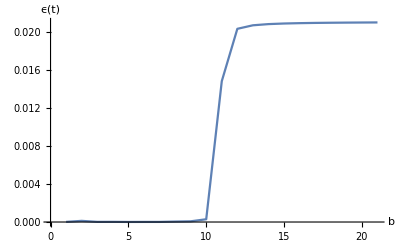

```mathematica
ListPlot[ϵlistGivenT,AxesLabel->{"b","ϵ(t)"},Joined->True,Ticks->{None,Automatic}]
```

## Evaluate ergodic metric for ranges of b and T

```mathematica
ϵlist={};
For[Tcounter=-1,Tcounter<3,Tcounter++;
T=10^Tcounter;
Print["T = ",T];
ϵlistGivenT={};
For[damping=-1.1,damping<1,damping=damping+0.1;
Print["damping = ",damping];
sol=NDSolve[{ssm/.b->damping,ICs},{x},{t,0,T},Method->{"FixedStep",Method->"ExplicitRungeKutta"}];
xt=x/.First[sol];
x1t=ListInterpolation[Flatten[xt["ValuesOnGrid"][[All,1]]],{0,T}];
x2t=ListInterpolation[Flatten[xt["ValuesOnGrid"][[All,2]]],{0,T}];
ϵ=ErgodicMetric[{{x1t},{x2t}}];
Print["ϵ = ",ϵ];
AppendTo[ϵlistGivenT,ϵ]
]
AppendTo[ϵlist,ϵlistGivenT]]
```

Generate plot

```mathematica
(*Get["CustomTicks`"];*)
ListPlot3D[{ϵlist},Ticks->{None,None,None},AxesLabel->{"b","T","ϵ"}]
```

-Graphics3D-